# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2023/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Library/CloudStorage/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
<<LineCableParam2020`
```

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=95. 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 138kV -- 138CST1

Dados dos condutores -- código desenvolvido pelo Prof. Robson Dias

### Dados do condutor

```mathematica
Nome=ToUpperCase["dove"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[18]

1)  Nome comercial = DOVE

2)  Bitola (MCM) = 556.5

3)  Num. de Fios de Al. = 26

4)  Diâmetro dos Fios de Al. (mm) = 3.716

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 2.891

7)  Seção transversal de Al (mm^2) = 281.98

8)  Seção transversal do cond. (mm^2) = 327.9

9)  Diâmetro do cond. (mm) = 23.54

10)  Diâmetro da Alma de Aço (mm) = 8.67

11)  Peso Nominal do Al (aprox.) (kg/km) = 781.2

12)  Peso nominal do Aço (aprox.) (kg/km) = 358.9

13)  Massa (aprox.) (kg/km) = 1140.2

14)  Carga de ruptura (Classe A) (kgf) = 10274

15)  Carga de ruptura (Classe B) (kgf) = 9959

16)  Ampacidade (A) = 730

17)  Raio médio geométrico (m) = 0.0955

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.102

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.123

20)  Reatância indutiva (Ohm/km) = 0.3508

21)  Reatância capacitiva (Mohm/km) = 0.2121

### Dados condutores de fase (Dove)

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdc=(dadoscond[[pos,19]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.35; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
```

```mathematica
(*flecha em metro *)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

7.30891

### Cabos guarda ou cabos pararraios (3/8 EHS)

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro*)
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)
```

3.59829

```mathematica
npr =2;
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

### Cabos guarda ou cabos pararraios (OPGW)

```mathematica
Tpr2=101.9 101.972; (*{kgf]*)
Wpr2=724; (*[kg/km]*)
Hpr2=0.25*Tpr2;
Ccatpr2=Hpr2/Wpr2;
(*flecha em metro*)
flechapr2=1000*Ccatpr2*(Cosh[svao/(2*Ccatpr2)]-1)
```

4.2685

```mathematica
rpr2=14.70/2*10^-3;
Rdcpr2= 0.511*10^-3;
```

## Visualiza Circuito

```mathematica
xc={3.4,-3.4,3.4, 3.4,-3.4};
yc=24.5-{3.8,3.8+1.9,3.8+3.8, 0,0};
fl=Join[flechacond{1, 1, 1},flechapr{1,1}];
yc= yc-2/3 fl;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,PlotRange->{{-5,5},{5,25.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
ω= 2. π 60;
ρs= 1000.;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,r1,r0, npr, Rdcpr,rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.230733+0.89487 ⅈ | 0.105251+0.399515 ⅈ | 0.103786+0.447568 ⅈ
0.105251+0.399515 ⅈ | 0.227088+0.898126 ⅈ | 0.102015+0.402443 ⅈ
0.103786+0.447568 ⅈ | 0.102015+0.402443 ⅈ | 0.224129+0.900797 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+3.01776×10^-6 ⅈ | 0.-3.46628×10^-7 ⅈ | 0.-6.26977×10^-7 ⅈ
0.-3.46628×10^-7 ⅈ | 3.×10^-9+2.92118×10^-6 ⅈ | 0.-3.40794×10^-7 ⅈ
0.-6.26977×10^-7 ⅈ | 0.-3.40794×10^-7 ⅈ | 3.×10^-9+3.02843×10^-6 ⅈ)

```mathematica
Zs =1000 (Zmat[[1,1]]+Zmat[[2,2]]+Zmat[[3,3]])/3
```

0.227317+0.897931 ⅈ

```mathematica
Zm = 1000(Zmat[[1,2]]+ Zmat[[1,3]]+Zmat[[2,3]])/3
```

0.103684+0.416509 ⅈ

```mathematica
Zabc = Table[If[i!= j, Zm, Zs],{i,1,3},{j,1,3}];
MatrixForm[Zabc ]
```

(0.227317+0.897931 ⅈ | 0.103684+0.416509 ⅈ | 0.103684+0.416509 ⅈ
0.103684+0.416509 ⅈ | 0.227317+0.897931 ⅈ | 0.103684+0.416509 ⅈ
0.103684+0.416509 ⅈ | 0.103684+0.416509 ⅈ | 0.227317+0.897931 ⅈ)

```mathematica
Ys =1000 (Ymat[[1,1]]+Ymat[[2,2]]+Ymat[[3,3]])/3
```

3.×10^-9+2.98912×10^-6 ⅈ

```mathematica
Ym = 1000(Ymat[[1,2]]+ Ymat[[1,3]]+Ymat[[2,3]])/3
```

0.-4.38133×10^-7 ⅈ

```mathematica
Yabc = Table[If[i!= j, Ym, Ys],{i,1,3},{j,1,3}];
MatrixForm[Yabc ]
```

(3.×10^-9+2.98912×10^-6 ⅈ | 0.-4.38133×10^-7 ⅈ | 0.-4.38133×10^-7 ⅈ
0.-4.38133×10^-7 ⅈ | 3.×10^-9+2.98912×10^-6 ⅈ | 0.-4.38133×10^-7 ⅈ
0.-4.38133×10^-7 ⅈ | 0.-4.38133×10^-7 ⅈ | 3.×10^-9+2.98912×10^-6 ⅈ)

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012= Inverse[A].Zabc. A;
MatrixForm[Z012]
```

(0.434685+1.73095 ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ
-6.93889×10^-17+4.16334×10^-17 ⅈ | 0.123633+0.481422 ⅈ | 5.55112×10^-17+6.93889×10^-18 ⅈ
-8.32667×10^-17+4.16334×10^-17 ⅈ | 2.77556×10^-17+0. ⅈ | 0.123633+0.481422 ⅈ)

```mathematica
MatrixForm[1000Inverse[A].Zmat.A]
```

(0.434685+1.73095 ⅈ | -0.0121002+0.00422501 ⅈ | 0.0171853+0.00677926 ⅈ
0.0171853+0.00677926 ⅈ | 0.123633+0.481422 ⅈ | 0.0270123-0.0156045 ⅈ
-0.0121002+0.00422501 ⅈ | -0.026933-0.0155877 ⅈ | 0.123633+0.481422 ⅈ)

comparando os resultados dos termos da diagonal

```mathematica
Diagonal[1000Inverse[A].Zmat.A] -Diagonal[Z012]
```

{5.55112×10^-17+4.44089×10^-16 ⅈ,5.55112×10^-17-1.11022×10^-16 ⅈ,5.55112×10^-17-5.55112×10^-17 ⅈ}

```mathematica
Y012= Inverse[A].Yabc. A;
MatrixForm[Y012*1000]
```

(3.×10^-6+0.00211286 ⅈ | 1.05879×10^-19+2.64698×10^-19 ⅈ | 2.11758×10^-19+2.64698×10^-19 ⅈ
-2.11758×10^-19-2.11758×10^-19 ⅈ | 3.×10^-6+0.00342726 ⅈ | 0.-1.05879×10^-19 ⅈ
-2.11758×10^-19-2.11758×10^-19 ⅈ | 0.-1.05879×10^-19 ⅈ | 3.×10^-6+0.00342726 ⅈ)

```mathematica
Z0= Z012[[1,1]]
```

0.434685+1.73095 ⅈ

```mathematica
Zpos= Z012[[2,2]]
```

0.123633+0.481422 ⅈ

```mathematica
Y0=Y012[[1,1]]
```

3.×10^-9+2.11286×10^-6 ⅈ

```mathematica
Ypos=Y012[[2,2]]
```

3.×10^-9+3.42726×10^-6 ⅈ

```mathematica
Zc= Sqrt[Zpos/Ypos]
```

377.84-47.5735 ⅈ

```mathematica
Pn = 138^2/Zc
```

49.6157+6.24706 ⅈ

## Avaliação do desequilibrio do circuito

```mathematica
Ztotal=Zmat ℓ + Re[Zc]DiagonalMatrix[{1,1,1}];
MatrixForm[Ztotal]
```

(399.76+85.0126 ⅈ | 9.99883+37.9539 ⅈ | 9.85966+42.519 ⅈ
9.99883+37.9539 ⅈ | 399.414+85.322 ⅈ | 9.69147+38.2321 ⅈ
9.85966+42.519 ⅈ | 9.69147+38.2321 ⅈ | 399.133+85.5757 ⅈ)

```mathematica
aux=138 10^3/Sqrt[3]{1, a^2,a};
```

```mathematica
iabc=Inverse[Ztotal].aux
```

{203.551-23.645 ⅈ,-122.109-162.208 ⅈ,-80.3424+184.636 ⅈ}

```mathematica
Abs[iabc]
```

{204.919,203.033,201.359}

```mathematica
ang1=Table[Arg[iabc[[i]]]/π 180 ,{i,3}]
```

{-6.62594,-126.972,113.516}

```mathematica
ang2=Arg[iabc[[1]]]/π 180  +{0, -120, 120}
```

{-6.62594,-126.626,113.374}

```mathematica
ang2-ang1
```

{0.,0.346239,-0.141685}

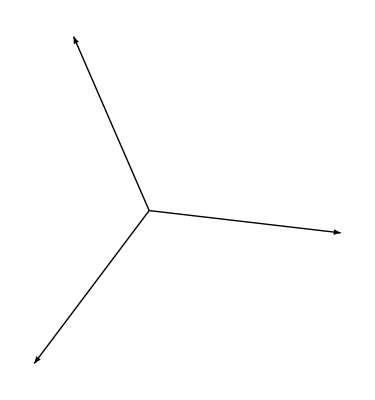

```mathematica
Graphics[Table[Arrow[{{0,0},{Re[iabc[[i]]],Im[iabc[[i]]] }}],{i,3}]]
```

### Cálculo das tensões de sequência

```mathematica
vabcL=  Re[Zc]DiagonalMatrix[{1,1,1}].iabc
```

{76909.6-8934.03 ⅈ,-46137.8-61288.9 ⅈ,-30356.6+69762.9 ⅈ}

```mathematica
Abs[vabcL ]
```

{77426.8,76713.9,76081.5}

```mathematica
v012=Inverse[A].vabcL
```

{138.409-153.32 ⅈ,76217.-8946.01 ⅈ,554.22+165.293 ⅈ}

### Cálculo dos desequilibrios de tensão

```mathematica
Table[100 Abs[v012[[i]]/v012[[2]]],{i,3}]
```

{0.269158,100.,0.753639}

A tensão de sequência zero é menor que 0,3%, e de sequência negativa menor que 1%